```mathematica
dividedDiff[nodes_,values_]:=(
If[Length[nodes]==1,
values[[1]],
(dividedDiff[nodes[[2;;Length[nodes]]],values[[2;;Length[nodes]]]]-dividedDiff[nodes[[1;;Length[nodes]-1]],values[[1;;Length[nodes]-1]]])/(nodes[[Length[nodes]]]-nodes[[1]])]
)
newtonPoly[nodes_,values_,x_]:=(
poly=0;
product=1;
For[i=1,i≤Length[nodes],i++,
poly+=dividedDiff[nodes[[1;;i]],values[[1;;i]]]*product;
product*=x-nodes[[i]]
];
poly//Expand
)
```

```mathematica
newtonPoly[{0,1,2,3},{0,2,12,36},x]
```

x^2+x^3

```mathematica
Zad1[x_] = newtonPoly[{1920, 1930, 1940, 1950, 1960, 1970, 1980, 1990},
					{106.46, 123.08, 132.12, 152.27, 180.67, 205.05, 227.23, 249.46}, x]
```

1.03999×10^14-3.7297×10^11 x+5.73221×10^8 x^2-489420. x^3+250.712 x^4-0.0770556 x^5+0.0000131566 x^6-9.62698×10^-10 x^7

```mathematica
Map[Zad1, {1952, 1974, 2000}]
```

{157.5,213.,175.}

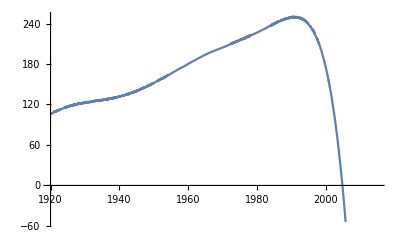

```mathematica
graph = Plot[Zad1[x] , {x, 1920, 2015}]
```

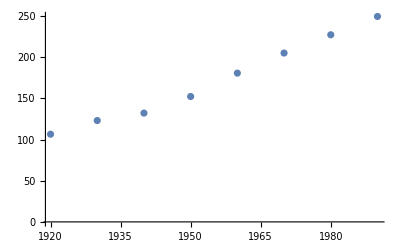

```mathematica
dots = ListPlot[{{1920, 106.46}, {1930, 123.08}, {1940, 132.12}, {1950, 152.27}, {1960, 180.67}, {1970, 205.05}, {1980, 227.23}, {1990, 249.46}}]
```

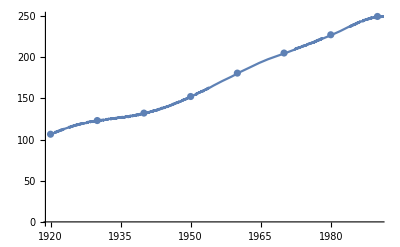

```mathematica
Show[dots, graph]
```

```mathematica
Zad3[x_] := newtonPoly[{0, 0.2, 0.4}, {0, 0.5, 0.8}, x]
```

```mathematica
Animate[Graphics[Circle[{x, Zad3[x]}, 0.1], Axes->True, AxesOrigin->{0, 0}, PlotRange->{{-0.5, 1}, {-0.5, 1}}], {x, 0, 0.4, 0.001}]
```